### Definition

```mathematica
a=Rationalize@0.5;
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=Rationalize@0.1;u0=10^-20;δstart=10^-10;m=10;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- α/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-1/20,-1/80,-1/180,-1/320,-1/500,-1/720,-1/980,-1/1280,-1/1620,-1/2000,-1/2420,-1/2880,-1/3380,-1/3920,-1/4500,-1/5120,-1/5780,-1/6480,-1/7220,-1/8000}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{ef,evShifted},
PrintTemporary[V];
Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
Table[
PrintTemporary[n];
Module[{sol,evnew,steps=∞,time1,time2},
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.
FindRoot[u[e][min]==0/.sol,If[n<5,{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[evShifted],{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[Table20REE]],opt2(*,StepMonitor:>PrintTemporary[e]*)]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt(*,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}*)],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543993347760223196461771012599211978) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00214659701500736348106511612925132078575082624619) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217594907690330015266210750673120987467033445067) is less than WorkingPrecision (50.).

```mathematica
Get["D:\\Documents\\Coulomb_psir_comparasion_a=0.5.mx"]
```

### Determine c_1

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end___},opt___]:=Module[{aaa,findroot,mon},aaa=a;
Print[aaa];
Monitor[findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>{mon={c1,evnhhhc1[c1]}}],mon];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},{MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50}]
```

0.1

NDSolve::precw: The precision of the differential equation ({{20 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000682475643443809801038864984663202512734798605464) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.634936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000676980199376761675928131128901388010769670272257) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.634936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000676980199376761675928131128901388010769670272257) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-0.69202747389763147323087738870043965968435665340985

-0.69202747389763147323087738870043965968435665340985

#### Vs_1’s eigensystem

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
N[%,6]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$6977]-u''[r$6977]/20==e$6976 u[r$6977],u'[Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]]==-1/1000000000000000,u[Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]]==1/1000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.0500079,-0.0125002,-0.00555559,-0.00312501,-0.002,-0.00138889,-0.00102041,-0.00078125,-0.000617284,-0.0005,-0.000413223,-0.000347222,-0.000295858,-0.000255102,-0.000222222,-0.000195313,-0.000173011,-0.000154327,-0.000138443,-0.000124049}

```mathematica
efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];
```

LinkOpen::linke: Unknown MathLink problem encountered..

General::stop: Further output of LinkOpen::linke will be suppressed during this calculation.

SubKernels`RemoteKernels`LaunchRemote::somefail: 4 of 4 kernels failed to launch.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0500078698243857713717887787042 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555558766918011422453272884499 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0020000024955053743545081067507 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102040862718159308255476878961 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000617284082651037425612626405505 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000500000077962926767212370479046 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000413223188903938764724442381674 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000347222253552894468125638263566 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

$Aborted

#### ψ_r Vs_1

```mathematica
IntegrationVs11st=NIntegrate[efVs1[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20;
```

```mathematica
ψrTrueVs1[n_][γ_,η_]:=4π(γ Integration1st[[n]])
```

```mathematica
DetermineVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[n,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs1[#][γ,η]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{r0,γ}(*,N[ERROR,6]*)/.RES
]
```

```mathematica
Determine[0]
```

```mathematica
Module[{γη},
γlVs1={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γlVs1,γη];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
γrVs1=Interpolation[γlVs1]
```

```mathematica
ψrfunVs1[r_][n_]:=4π(γrVs1[r] IntegrationVs11st[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

### Determine c_2 & d_1

```mathematica
Exit
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[10^-9,c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1[{c2start_,c2end___},{d1start_,d1end___}]:=Module[{findroot,mon},
Monitor[findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[10^-9,c2,d1]==δexpminus9},{{c2,c2start,c2end},{d1,d1start,d1end}},MaxIterations->100,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>{mon={c2,d1,evnhhh1,evnhhh2}}],mon];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1[{1},{-1}]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000750834791513318113425945394650823415401066435317) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00237435159640123390752606756471540890279883432478) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000750834791513318113425945394650823415401066435317) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ReplaceAll::reps: {findroot$42705} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {c2,d1} and {c2,d1}/.findroot$42705 are not the same shape.

{c2,d1}/.findroot$42705

```mathematica
evnhhh1
evnhhh2
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543993342770315118903596600422281145) is less than WorkingPrecision (50.).

4.9899058×10^-24

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00214659701500736348106691080347300466559605386771) is less than WorkingPrecision (50.).

-1.794666×10^-24

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Coulomb_psir_comparasion_a=0.5.mx",{c2,d1}]
```

{-0.47324684669335419909233441643436893243578721913311,0.41332364452155442416475236855754267025005147764448}

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,2000},{-0.0004995,-0.0005005},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,StartingStepSize->10^-4,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

{-0.000499368368687840637445103170283,2.4235025452000346205322709528×10^-15}time:57.661189s

{-0.000499483597607165470318759610789,-1.210816798009673308635839964×10^-15}time:18.591117s

{-0.000499506535194088818936574545903,-3.574849429862691810208493718×10^-16}time:18.802769s

{-0.000499319766362374863826423164164,-1.880429208151421775032392703×10^-16}time:19.20105s

{-0.000499103804212978790828943890064,-2.7613301439935461768415238287×10^-15}time:19.462733s

{-0.000499335547792831660599391627545,-1.4308836775633069580397230622×10^-15}time:16.333025s

{-0.000499317378617797270748018866906,4.5589973771365064325570631996×10^-15}time:11.232424s

{-0.000499319671777446919384173989217,-3.7710610869059557133534235558×10^-15}time:16.738796s

{-0.000499319771326353635714091557773,-1.171036398845380470038722303×10^-15}time:21.488663s

{-0.000499319765412784568476156808905,7.54006222555780610659049222×10^-18}time:25.058683s

{-0.000499319765449392916525725439264,-2.7631146933902024308495382518×10^-15}time:24.139032s

{-0.000499319765412884194465901344757,-4.0176766341410733570083113834×10^-15}time:23.25291s

{-0.00049931976541278475509621198125,-4.3001936309572518238289036539×10^-15}time:22.543908s

{-0.000499319765412784568802808112992,-4.0998954804185563701785146415×10^-15}time:20.338349s

{-0.000499319765412784568476756446108,4.154901418840236932603221862×10^-16}time:20.362371s

{-0.000499319765412784568476756446108}

```mathematica
(%+0.0005)/0.0005
```

{0.00136047}

#### Vs_2’s eigensystem

```mathematica
AbsoluteTiming[energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{10^-15,Which[n<10,1000,10≤n<15,2000,15≤n<19,4000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]]
```

{-0.0496266,-0.0124976,-0.00555542,-0.00312498,-0.00199999,-0.00138889,-0.00102041,-0.000781249,-0.000617284,-0.0005,-0.000413223,-0.000347222,-0.000295858,-0.000255102,-0.000222222,-0.000195312,-0.00017301,-0.000154321,-0.000138504,-0.000125}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{8300.53,{-0.0496267886275482868777804414966,-0.0124976627516604027387337463388,-0.00555542459542951527514777362788,-0.00312498278398785508087162703801,-0.00199999641497397909469169711818,-0.00138888789220705935983362204121,-0.00102040782525947684178178632023,-0.000781249867465609015713001944831,-0.000617283892565699925762955431484,-0.000499999972254528582219013403948,-0.000413223126265799441902315907526,-0.000347222214486384101677989942898,-0.000295857983749641972508203125309,-0.000255102038188302951546560883694,-0.000222222220601168728220323819043,-0.000195312498968371780365942496,-0.000173010379948060610283709940581,-0.000154320987202106576140485034667,-0.000138504154814958904370328270139,-0.000124999999783746774022819568896}}

```mathematica
(energyVs2-Table20REE)/Table20REE
```

{-0.00746422744903426244439117007,-0.0001869798671677809013002929,-0.00002357282268725047340074698,-5.50912388637412107934784×10^-6,-1.79251301045265415144091×10^-6,-7.1761091726091979213033×10^-7,-3.3124571269505384940618×10^-7,-1.6964402045988735751062×10^-7,-9.4043566120264012201×10^-8,-5.54909428355619731921×10^-8,-3.443676535059639550379×10^-8,-2.227921378716738896445×10^-8,-1.492621013292227343646×10^-8,-1.030185242993748133592×10^-8,-7.29474072300854281431×10^-9,-5.28193648452637442048×10^-9,-3.90020967256015654344×10^-9,-2.93034938660965697536×10^-9,-2.2359967104462298896×10^-9,-1.73002580781744344883×10^-9}

```mathematica
efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<11,2000,11≤n<15,3000,15≤n<19,4000,n≥19,6000],If[n<12,1.*10^-40,1.*10^-30]},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];
```

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0496267886275482868777804414966 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00312498278398785508087162703801 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102040782525947684178178632023 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000499999972254528582219013403948 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000781249867465609015713001944831 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000413223126265799441902315907526 f[r],f[3000]==1.×10^-40,f'[3000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00199999641497397909469169711818 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0124976627516604027387337463388 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000617283892565699925762955431484 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000347222214486384101677989942898 f[r],f[3000]==1.×10^-30,f'[3000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00138888789220705935983362204121 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555542459542951527514777362788 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000295857983749641972508203125309 f[r],f[3000]==1.×10^-30,f'[3000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000222222220601168728220323819043 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010379948060610283709940581 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504154814958904370328270139 f[r],f[6000]==1.×10^-30,f'[6000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000255102038188302951546560883694 f[r],f[3000]==1.×10^-30,f'[3000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000195312498968371780365942496 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000154320987202106576140485034667 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000124999999783746774022819568896 f[r],f[6000]==1.×10^-30,f'[6000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.060096325981950762891479383725856535597167762189563 Power[«2»]+0.02583272778259715151029702303484641689062821735278 Plus[«2»]-1/10 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0124976627516604027387337463388 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{6.075962543771×10^-380                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r]}

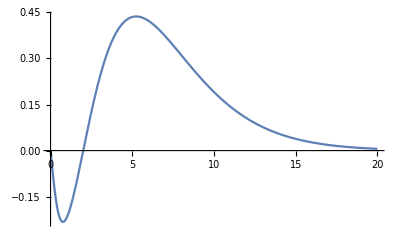

```mathematica
Module[{n=2},Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{2000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4(*,StartingStepSize->10^-6*)]]
Plot[%,{r,0,20},AxesOrigin->{0,0},PlotRange->Full]
```

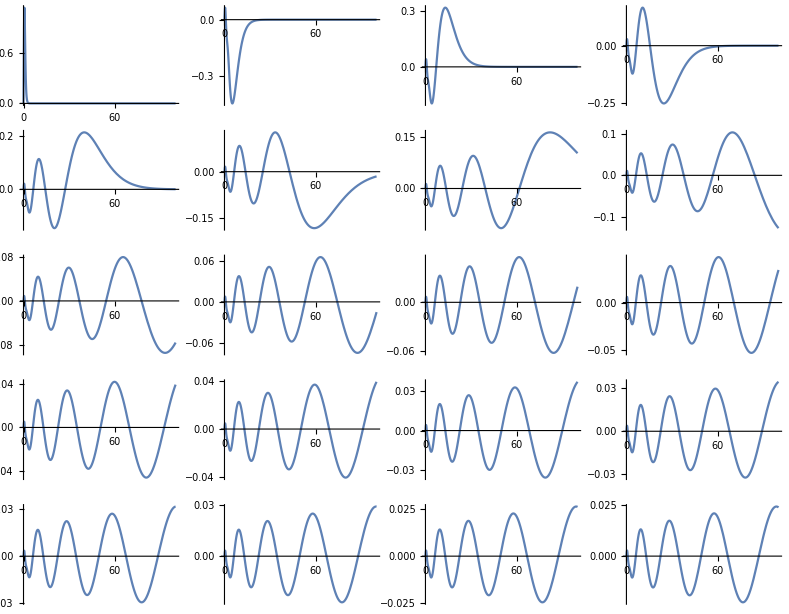

```mathematica
GraphicsGrid@Partition[Plot[efVs2[[#]],{r,0,100},ImageSize->Small,AxesOrigin->{0,0},PlotRange->Full]&/@Range@20,4]
```

#### ψ_r Vs_2

```mathematica
NIntegrate[efVs2[[1]]/(√(4π)r)δa[r] r^2,{r,0,2000},WorkingPrecision->30,AccuracyGoal->10]
```

NIntegrate::precw: The precision of the argument function (9.02795430375×10^-825 ⅇ^(-2 r^2) r «1») is less than WorkingPrecision (30.).

3.43890051025574127270699202141×10^-17

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30]&/@Range@20
```

NIntegrate::precw: The precision of the argument function (9.02795430375×10^-825 ⅇ^(-2 r^2) r «1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-1.35484332371×10^-390 ⅇ^(-2 r^2) r «1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (1.54265×10^-243 ⅇ^(«1») r InterpolatingFunction[{{9.9999999999999992929287939988014500233064511906197×10^-41,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«23370»},{NDSolve`LocalSeries,«49»,«23370»}}}][r]) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.0213186925583196672377863203656,0.00677780967406178860380464994038,0.00360953049992616752862462151952,0.00232647030648082013206011522016,0.00165875689300159781791180100391,0.00125941506779733793498702129588,0.000998253882482847568299830679986,0.000816438710222766564539841757578,0.000683862690204702732901460382476,0.000583675011450448327388481440755,0.000505781022884761359852398008432,0.000443801504367352856469988666199,0.000393527291066955975057436070455,0.000352080271522396099292540950396,0.000317432628246809232868556898413,0.000288118677873627676357129169464,0.000263055438994594721100045983142,0.000241427183236618153824187384936,0.000222609009740089215615873065248,0.000206114974696938838052154780809}

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (3.03702×10^-243 r («1») InterpolatingFunction[{{9.9999999999999992929287939988014500233064511906197×10^-41,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«23370»},{NDSolve`LocalSeries,«49»,«23370»}}}][r]) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-0.0578057146990411305874775515049,-0.0243632378221202928281342399698,-0.0135740635489553268752331263443,-0.00888438623226609961922902449937,-0.00637921840311269319001417267505,-0.0048618824676041325301132227312,-0.00386250533767327009400793812789,-0.00316369562287724565507286048678,-0.00265265239668517074670923690559,-0.00226567303593268300245468060284,-0.00196436130118958394842714586361,-0.00172434642064939145677185164567,-0.00152949561474491231278024720049,-0.00136875035992374214347869944292,-0.00123430412152573020527315136033,-0.0011205057357967703617657217076,-0.00102317440276684609105391121439,-0.000939157821758863183253796267423,-0.000866039075158727271122378005725,-0.000801937346273171295436124770013}

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[#,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

{{0,1.18216991137941053619648213775},{0,-1.28837169648338082004853750653}}

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: The precision of the argument function ({4 π (0.000317432628246809232868556898413 γ-0.000308576030381432551318287840083 η)==0.00971154,4 π (0.000206114974696938838052154780809 γ-0.000200484336568292823859031192503 η)==0.00630783}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (0.000317432628246809232868556898413 γ-0.000308576030381432551318287840083 η)==0.00970183,4 π (0.000206114974696938838052154780809 γ-0.000200484336568292823859031192503 η)==0.00630153}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (0.000317432628246809232868556898413 γ-0.000308576030381432551318287840083 η)==0.00969213,4 π (0.000206114974696938838052154780809 γ-0.000200484336568292823859031192503 η)==0.00629522}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

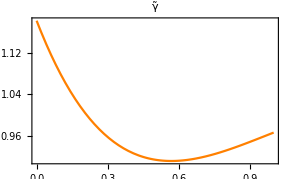
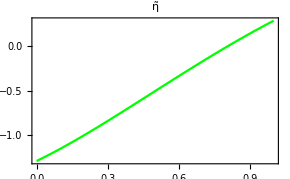
a=0.5
-Graphics-
-Graphics-

C:\Users\yingsheng\OneDrive\Documents\Test_6\Coulomb_psir_comparasion_a=0.5gammaeta.eps

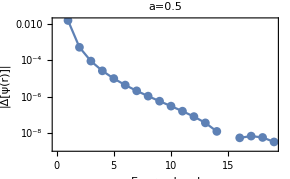

C:\Users\yingsheng\OneDrive\Documents\Test_6\Coulomb_psir_comparasion_a=0.5error.eps

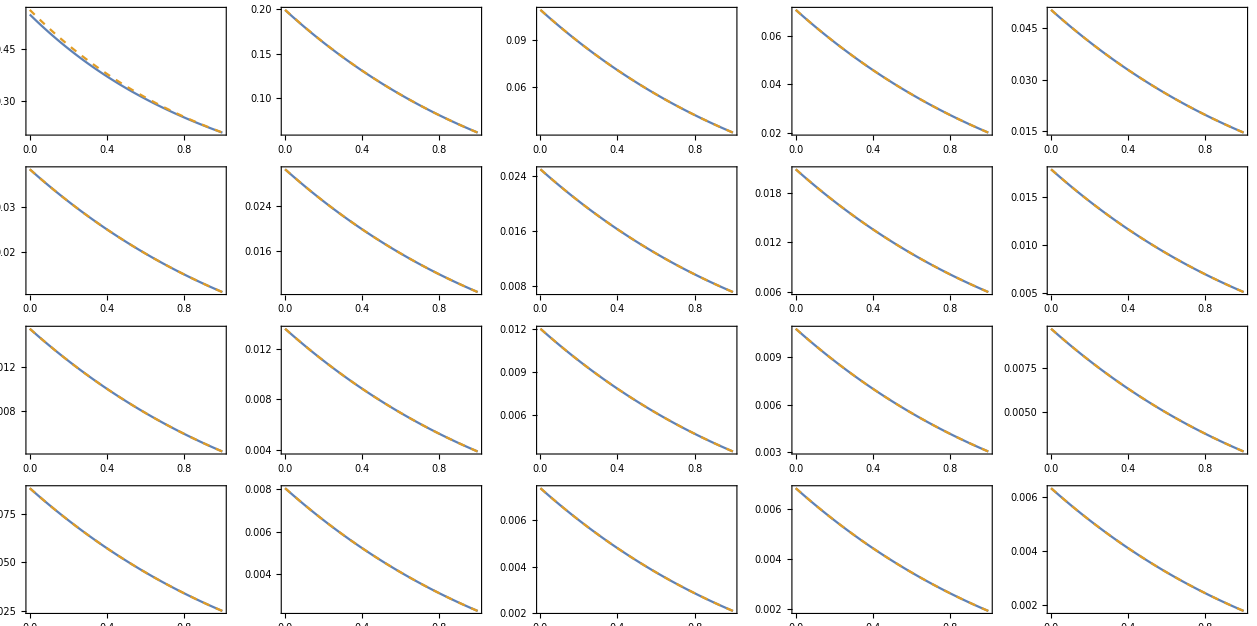

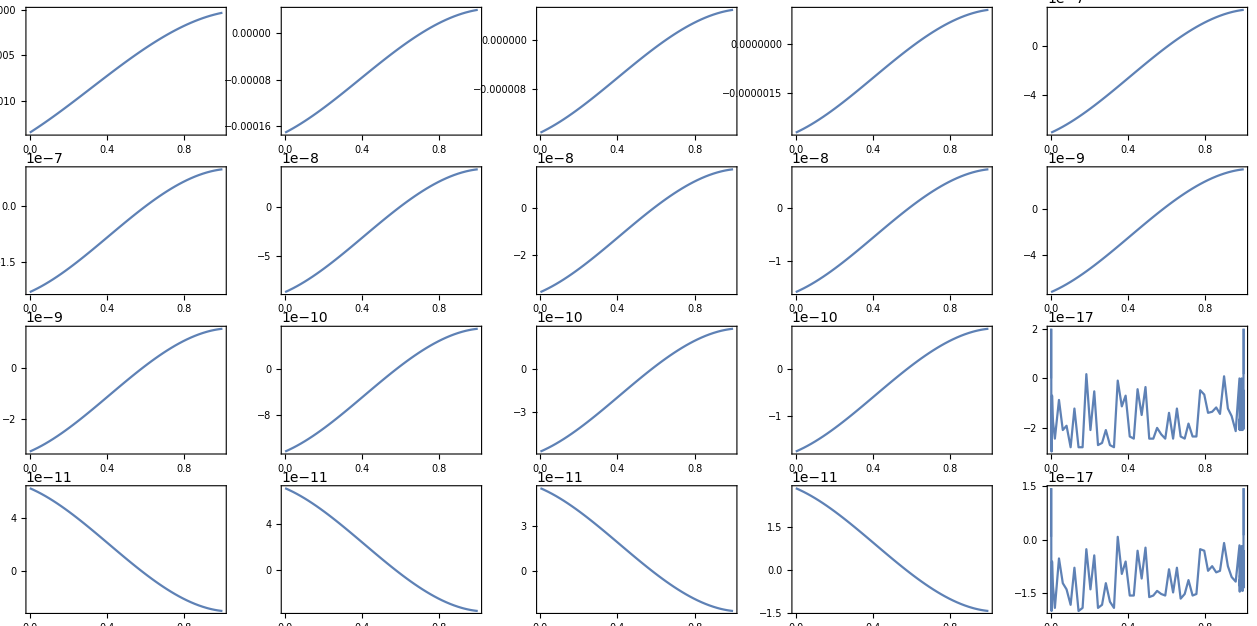

```mathematica
Column[{Style["a="<>ToString[N@a],18],Plot[γrVs2[r],{r,0,1},ImageSize->290,PlotStyle->Orange,PlotLabel->Style["γ̃",15],Frame->True,Axes->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}},PlotRange->{{0,Automatic},Automatic}],Plot[ηrVs2[r],{r,0,1},ImageSize->290,PlotStyle->Green,PlotLabel->Style["η̃",15],Frame->True,Axes->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}},PlotRange->{{0,Automatic},Automatic}]},Center]
Export[NotebookDirectory[]<>"Test_6\\"<>FileBaseName[NotebookFileName[]]<>"gammaeta.eps",%]
ListLogPlot[ReplacePart[Table[Mean[Table[Abs[(ψrfunVs2[r][n]-RS[n,r]/(√(4π)))/(RS[n,r]/(√(4π)))],{r,0,1,0.01}]],{n,1,20}],{{15},{20}}->0],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->290,FrameLabel->Reverse@{"|Δ[ψ(r)]|","Energy level"},RotateLabel->True,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}},PlotLabel->Style["a="<>ToString[N@a],15]]
Export[NotebookDirectory[]<>"Test_6\\"<>FileBaseName[NotebookFileName[]]<>"error.eps",%]
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n]-RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
```

```mathematica
∇^2 Subscript[ψ, r] Subscript[Vs, 1]
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]]
```

```mathematica
lappsi=lap[efVs2[[#]]/(√(4π)r),r]&/@Range@20;
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DeterminelapVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20},Tru},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[RS[#,r]/(√(4π)),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DeterminelapVs2[0.1]
```

FindRoot::precw: The precision of the argument function ({4 π (0.000317432628246809232868556898413 γ-0.000308576030381432551318287840083 η)==-0.175407,4 π (0.000206114974696938838052154780809 γ-0.000200484336568292823859031192503 η)==-0.113941}) is less than WorkingPrecision (30.).

{{0.1,-14.4631136487536378667871533187},{0.1,30.3567653238533304005675470966}}

```mathematica
Quiet@Module[{max=1,interval=0.001},
(*Zl=Determine[0][[1]];*)γllapVs2={};ηllapVs2={};
Monitor[Table[Module[{γη},
γη=DeterminelapVs2[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllapVs2,γη[[1]]];
AppendTo[ηllapVs2,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
γrlapVs2=Interpolation[γllapVs2]
ηrlapVs2=Interpolation[ηllapVs2]
```

InterpolatingFunction[{{0.01, 1.}}, <>]

InterpolatingFunction[{{0.01, 1.}}, <>]

```mathematica
ψrfunlapVs2[r_][n_]:=4π(γrlapVs2[r] IntegrationVs21st[[n]]+ηrlapVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
lapRS[n_,r_]=lap[RS[n,r]/(√(4π)),r];
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

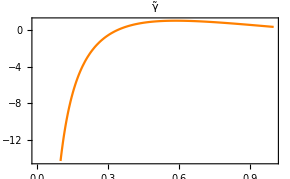
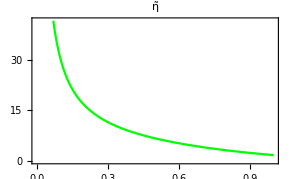
a=0.5
-Graphics-
-Graphics-

C:\Users\yingsheng\OneDrive\Documents\Test_6\Coulomb_psir_comparasion_a=0.5lapgammaeta.eps

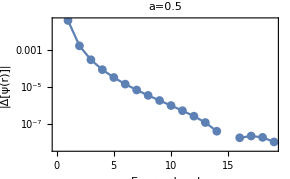

C:\Users\yingsheng\OneDrive\Documents\Test_6\Coulomb_psir_comparasion_a=0.5laperror.eps

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

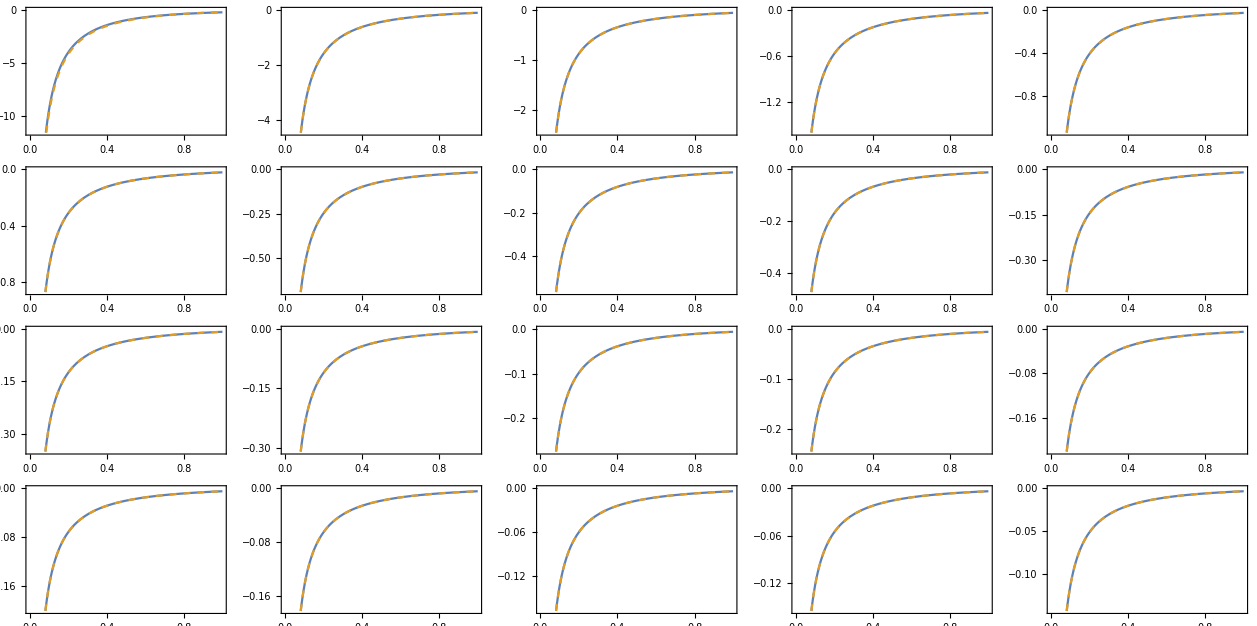

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

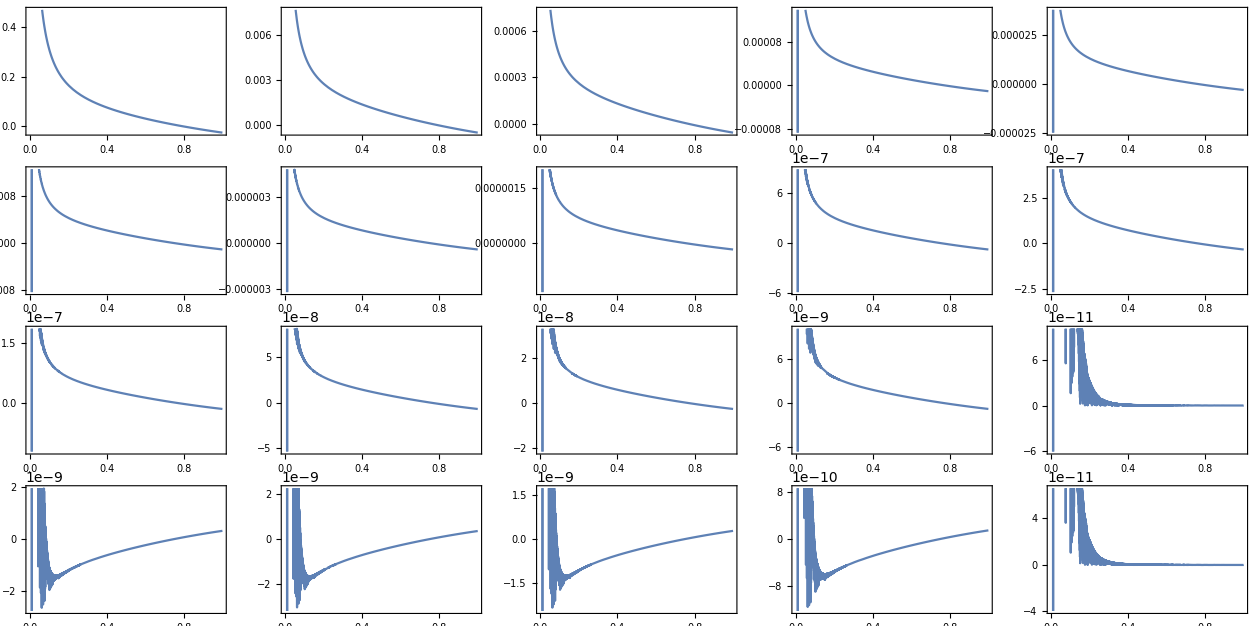

```mathematica
Column[{Style["a="<>ToString[N@a],18],Plot[γrlapVs2[r],{r,0,1},ImageSize->290,PlotStyle->Orange,PlotLabel->Style["γ̃",15],Frame->True,Axes->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}},PlotRange->{{0,Automatic},Automatic}],Plot[ηrlapVs2[r],{r,0,1},ImageSize->290,PlotStyle->Green,PlotLabel->Style["η̃",15],Frame->True,Axes->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}},PlotRange->{{0,Automatic},Automatic}]},Center]
Export[NotebookDirectory[]<>"Test_6\\"<>FileBaseName[NotebookFileName[]]<>"lapgammaeta.eps",%]
ListLogPlot[ReplacePart[Table[Mean[Table[Abs[(ψrfunlapVs2[r][n]-lapRS[n,r])/lapRS[n,r]],{r,0.01,1,0.01}]],{n,1,20}],{{15},{20}}->0],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->290,FrameLabel->Reverse@{"|Δ[ψ(r)]|","Energy level"},RotateLabel->True,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}},PlotLabel->Style["a="<>ToString[N@a],15]]
Export[NotebookDirectory[]<>"Test_6\\"<>FileBaseName[NotebookFileName[]]<>"laperror.eps",%]
GraphicsGrid@Partition[Table[Plot[{ψrfunlapVs2[r][n],lapRS[n,r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
GraphicsGrid@Partition[Table[Plot[{ψrfunlapVs2[r][n]-lapRS[n,r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
```